```mathematica
(* MVE2D.lib в папке MVE2D *)
```

```mathematica
k={0.0,0.0,1.0};
```

```mathematica
(*Параметры профиля Жуковского
a <- >  ширина крыла (во сколько раз увеличиваем радиус единичной окружности)
h < - > искривление (на сколько поднимаем окружность по мнимой оси)
d < - > толщина крыла (расстояние между центрами окружностей на КП - [ζ])
γ < - > искривление (угол наклона отрезка d  к отрицательному направлению оси Ох) *)
```

```mathematica
(* Окружность радиуса R *)
```

```mathematica
a1=4.0;
b=1.0;
ϵ=(√(a1^2-b^2))/a1
```

0.968246

```mathematica
a=a1 ϵ;
h=0.0;
d=0.0;
γ=ArcTan[h/a];
R=a1+b;
```

```mathematica
H=ⅈ h - d Exp[-ⅈ γ];
```

```mathematica
ζ[t_]:=ⅇ^(ⅈ t);
```

```mathematica
(* Циркуляция на профиле *)
```

```mathematica
(* угол атаки *)
β=-π/6;
```

```mathematica
GA[β_]=0.0;
```

```mathematica
(* Отображение z[ζ]: Окружность -> Контур *)
```

```mathematica
z[t_]:= 1/2* ( R ζ[t-γ] - d Cos[γ]+ⅈ (h+d Sin[γ])+ a^2/(R ζ [t-γ] - d Cos[γ]+ⅈ (h+d Sin[γ])))
```

```mathematica
r[t_]:= R Cos[t-γ]-d Cos[γ](* реальная часть *)
m[t_]:= R Sin[t-γ]+ d Sin[γ]+ h    (* мнимая часть *)
x[t_]:= FullSimplify[(r[t]*(r[t]^2+ m[t]^2+a^2))/(2 *(r[t]^2+ m[t]^2))]
y[t_]:=FullSimplify[ (m[t]*(r[t]^2+ m[t]^2-a^2))/(2 *(r[t]^2+ m[t]^2))]
(*figairfoil=ParametricPlot[{x[t],y[t]},{t,-Pi,  Pi},PlotStyle-> Thick, AxesOrigin ->{0,0} ,PlotRange-> All,AspectRatio->Automatic];
Show[figairfoil]*)
```

```mathematica
sumlen=NIntegrate[√((x'[t])^2+(y'[t])^2),{t,0,2π},AccuracyGoal->Infinity,PrecisionGoal->8,WorkingPrecision->16]
```

17.15684355001547

```mathematica
n=200; (*количество панелей*)
v0={N[Cos[β]],N[Sin[β]],0}(*скорость на бесконечности*)
```

{0.866025,-0.5,0}

```mathematica
dlen=sumlen/n;
```

```mathematica
derx[p_]:=D[x[t],t]/.t->p;
dery[p_]:=D[y[t],t]/.t->p;
```

```mathematica
dist0[tb_?NumberQ,te_?NumberQ]:=NIntegrate[√((derx[t])^2+(dery[t])^2),{t,tb,te}];
```

```mathematica
kk=Floor[n/1];
AbsoluteTiming[loclen=ParallelTable[dist0[(2.0π (i-1))/kk,(2.0π (i))/kk],{i,kk}]];
```

```mathematica
AbsoluteTiming[linlen={{0,0}}~Join~Table[{(2.0π (i))/kk,Plus@@loclen[[;;i]]},{i,kk}]];
```

```mathematica
interp=Interpolation[linlen,InterpolationOrder->5]
```

InterpolatingFunction[…]

```mathematica
AbsoluteTiming[tau={0}~Join~ParallelTable[w/.FindRoot[interp[w]==dlen j,{w,(2π j)/n},Method-> "Secant",MaxIterations->1000],{j,1,n-1}]];
```

```mathematica
tau=Append[tau,2.0π];
```

```mathematica
tau[[n+1]]
```

6.28319

```mathematica
(* Массив расчетных точек   -  ССz *)
```

```mathematica
CCz=Table[{0,0,0},{i,n+1}];
(*tk[i_]:=(2 π (i-0.5))/n;*)
tc[i_]:=(2 π (i-1.0))/n;(*Угловые параметры для точек рождения*)
(*For[i=1,i≤ n,KKz[[i]]={x[tk[i]],y[tk[i]]};i++];*)
For[i=1,i≤ n,CCz[[i]]={x[tau[[i]]],y[tau[[i]]],0};i++];
CCz[[n+1]]=CCz[[1]];
```

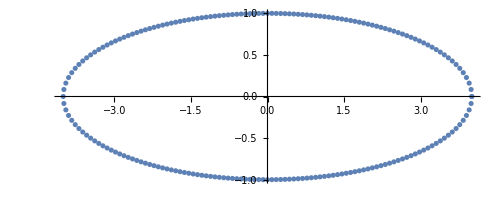

```mathematica
ListPlot[CCz[[All,1;;2]],AspectRatio->Automatic]
```

```mathematica
Длины панелей 
len=Table[0,{i,n}] ;
For[i=1,i≤ n,len[[i]]=√((CCz[[i]]-CCz[[i+1]]).(CCz[[i]]-CCz[[i+1]]));i++];
```

```mathematica
(* Нормали  - задаются линейно через ССz *)
```

```mathematica
2 π/(n-1)//N
```

0.0315738

```mathematica
Kas=Table[{0,0,0},{i,n}] ;
For[i=1,i≤ n,Kas[[i]]=(CCz[[i+1]]-CCz[[i]])/len[[i]];i++];
```

```mathematica
path=SetDirectory[NotebookDirectory[]];
libname=ToString[path]<>"\\";
FindLibrary[libname];
```

```mathematica
Matrnew=LibraryFunctionLoad[libname,"Matrc",{{Real,2},Integer},{Real,2}]
```

LibraryFunction[…]

```mathematica
CCzCrop=CCz[[1;;n,1;;2]];
```

```mathematica
time1cpp=AbsoluteTiming[
A33=Matrnew[CCzCrop,n];
]
```

{0.021421,Null}

```mathematica
LibraryFunctionUnload[Matrnew]
```

```mathematica
rhs=Table[0,{i,1,2n+1}];
```

```mathematica
For[i=1,i<n+1,i++,
(pod={τi->Kas[[i]]};
rhs[[i]]=-v0.(τi/.pod)
)]
```

```mathematica
rhs[[2n+1]]=GA[β];
```

```mathematica
rhs;
```

```mathematica
Resh = LinearSolve[A33,rhs];
```

```mathematica
(*Resh=(1/(len~Join~len))Flatten@Import["Ellipse1000pan-lin.txt","Table"][[1;;-2]];*)
```

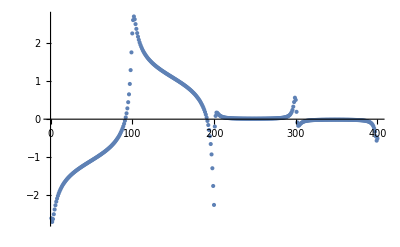

```mathematica
ListPlot[Resh[[1;;2n]]]
```

```mathematica
Xlens={0}~Join~Table[Sum[len[[j]],{j,1,i}],{i,1,n}];
```

```mathematica
SolNum[x_]:=(q=1;While[x>Xlens[[q+1]],q++];Resh[[q]]+Resh[[n+q]]*((x-Xlens[[q]])/Norm[CCz[[q+1]]-CCz[[q]]]-1/2))
```

```mathematica
SolNumT[t_?NumberQ]:=Module[{xt,yt,rt,q,St},
xt=x[t];yt=y[t];
 q=1;While[t>tau[[q+1]],q++];
rt={xt,yt,0}-CCz[[q]];
St=rt.Kas[[q]];
Resh[[q]]+Resh[[n+q]]*(St/len[[q]]-1/2)
]
```

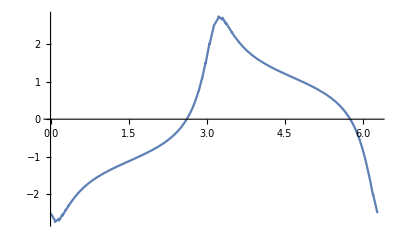

```mathematica
FigNumT=Plot[SolNumT[t],{t,0,2π}]
```

```mathematica
q=n;
p=n;
A33[[q+1;;q+3,p+1;;p+3]]//MatrixForm
```

(-0.0416667 | -0.00119579 | -0.000106011
-0.00119192 | -0.0416667 | -0.000864555
-0.000061277 | -0.000862444 | -0.0416667)

```mathematica
A33[[-1,All]];
```

```mathematica
rhs[[1;;3]]
```

{0.637113,0.832002,0.929979}

```mathematica
SolEx[t_]:=(2 Norm[v0] Sin[γ + β - t]+GA[t]/(π R))/Abs[1-a^2/(R Exp[ⅈ (t-γ)]+H)^2];
```

```mathematica
normV0=Norm[v0];
```

```mathematica
GAComp=Compile[{{normV0,_Real},{β,_Real},{γ,_Real},{h,_Real},{a,_Real},{d,_Real}},0(*-2π normV0 Sin[β + γ](√(h^2+a^2)+d)*),RuntimeOptions->"EvaluateSymbolically"->False,(*CompilationTarget->"C",*)Parallelization->Automatic];
```

```mathematica
SolExComp=Compile[{{a,_Real},{R,_Real},{d,_Real},{h,_Real},{β,_Real},{γ,_Real},{normV0,_Real},{t,_Real}},
Module[{znam=0.0},
(znam=√((4 a^4 (R Cos[t-γ]-d Cos[γ])^2 (-h-R Sin[t-γ]-d Sin[γ])^2)/((R Cos[t-γ]-d Cos[γ])^2+(h+R Sin[t-γ]+d Sin[γ])^2)^4+(1.-(a^2 ((R Cos[t-γ]-d Cos[γ])^2-(-h-R Sin[t-γ]-d Sin[γ])^2))/((R Cos[t-γ]-d Cos[γ])^2+(h+R Sin[t-γ]+d Sin[γ])^2)^2)^2);
1/znam(2.0 normV0 Sin[γ + β - t]+GAComp[normV0,β,γ,h,a,d]/(π R)))],RuntimeOptions->"EvaluateSymbolically"->False,(*CompilationTarget->"C",*)Parallelization->Automatic];
```

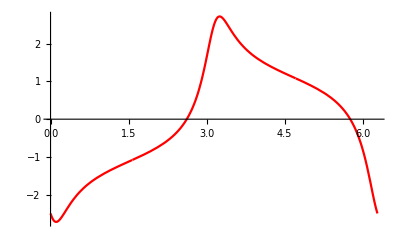

```mathematica
FigEx=Plot[SolEx[t],{t,0,2π},PlotRange->All,PlotStyle->Red]
```

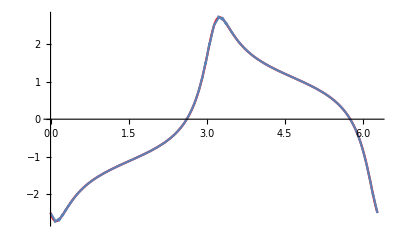

```mathematica
Show[{FigEx,FigNumT}]
```

```mathematica
Jac=Compile[
{{a,_Real},{R,_Real},{d,_Real},{h,_Real},{γ,_Real},{t,_Real}},
Module[{derx,dery},
(derx=0.5 (-R Sin[t-γ]-(a^2 (R Cos[t-γ]-d Cos[γ]) (2 h R Cos[t-γ]+2 d R Sin[t]))/(d^2+h^2+R^2-2 d R Cos[t]+2 h R Sin[t-γ]+2 d h Sin[γ])^2-(a^2 R Sin[t-γ])/(d^2+h^2+R^2-2 d R Cos[t]+2 h R Sin[t-γ]+2 d h Sin[γ]));
dery=(R (2 (h Cos[t-γ]+d Sin[t]) (h+R Sin[t-γ]+d Sin[γ]) (d^2+h^2+R^2-2 d R Cos[t]+2 h R Sin[t-γ]+2 d h Sin[γ])-2 (h Cos[t-γ]+d Sin[t]) (h+R Sin[t-γ]+d Sin[γ]) (-a^2+d^2+h^2+R^2-2 d R Cos[t]+2 h R Sin[t-γ]+2 d h Sin[γ])+Cos[t-γ] (d^2+h^2+R^2-2 d R Cos[t]+2 h R Sin[t-γ]+2 d h Sin[γ]) (-a^2+d^2+h^2+R^2-2 d R Cos[t]+2 h R Sin[t-γ]+2 d h Sin[γ])))/(2 (d^2+h^2+R^2-2 d R Cos[t]+2 h R Sin[t-γ]+2 d h Sin[γ])^2);
√(derx^2+dery^2)
)
],RuntimeOptions->"EvaluateSymbolically"->False,(*CompilationTarget->"C",*)Parallelization->Automatic
];
```

```mathematica
rComp= Compile[{{γ,_Real},{R,_Real},{d,_Real},{t,_Real}},
R Cos[t-γ]-d Cos[γ],RuntimeOptions->"EvaluateSymbolically"->False,(*CompilationTarget->"C",*)Parallelization->Automatic];(* реальная часть *)
mComp= Compile[{{γ,_Real},{R,_Real},{d,_Real},{t,_Real},{h,_Real}},R Sin[t-γ]+ d Sin[γ]+ h  ,RuntimeOptions->"EvaluateSymbolically"->False,(*CompilationTarget->"C",*)Parallelization->Automatic] ; (* мнимая часть *)
xComp=Compile[{{a,_Real},{γ,_Real},{R,_Real},{d,_Real},{t,_Real},{h,_Real}}, 1/2 rComp[γ,R,d,t] (1+a^2/(mComp[γ,R,d,t,h]^2+rComp[γ,R,d,t]^2)),RuntimeOptions->"EvaluateSymbolically"->False,(*CompilationTarget->"C",*)Parallelization->Automatic];
yComp=Compile[{{a,_Real},{γ,_Real},{R,_Real},{d,_Real},{t,_Real},{h,_Real}}, 1/2 mComp[γ,R,d,t,h] (1-a^2/(mComp[γ,R,d,t,h]^2+rComp[γ,R,d,t]^2)),RuntimeOptions->"EvaluateSymbolically"->False,(*CompilationTarget->"C",*)Parallelization->Automatic];
```

```mathematica
SolNumTComp=Compile[{{n,_Integer},{tau,_Real,1},{len,_Real,1},{CCz,_Real,2},{Kas,_Real,2},{Resh,_Real,1},{a,_Real},{γ,_Real},{R,_Real},{d,_Real},{t,_Real},{h,_Real}},
Module[{xt=0.0,yt=0.0,rt={0.0,0.0,0.0},q=1,St=0.0},
xt=xComp[a,γ,R,d,t,h];yt=yComp[a,γ,R,d,t,h];
 While[t>tau[[q+1]],q++];
rt={xt,yt,0.0}-CCz[[q]];
St=rt.Kas[[q]];
Resh[[q]]+Resh[[n+q]]*(St/len[[q]]-0.5)
],RuntimeOptions->"EvaluateSymbolically"->False,(*CompilationTarget->"C",*)Parallelization->Automatic];
```

```mathematica
SolNumT[t_?NumberQ]:=Module[{xt,yt,rt,q,St},
xt=x[t];yt=y[t];
 q=1;While[t>tau[[q+1]],q++];
rt={xt,yt,0}-CCz[[q]];
St=rt.Kas[[q]];
Resh[[q]]+Resh[[n+q]]*(St/len[[q]]-1/2)
]
```

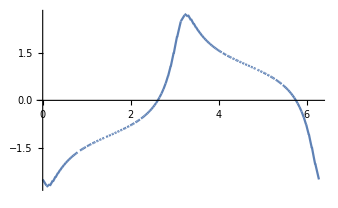

```mathematica
FigNumT=Plot[SolNumT[t],{t,0,2π},Exclusions->tau,PlotPoints->200]
```

```mathematica
(*deltaL1=ParallelTable[Quiet@NIntegrate[Abs[SolExComp[a,R,d,h,β,γ,normV0,ξ]-SolNumTComp[n,tau,len,CCz,Kas,Resh,a,γ,R,d,ξ,h]]Jac[a,R,d,h,γ,ξ],{ξ,tau[[i]],tau[[i+1]]}],{i,1,n}];*)
```

```mathematica
(*err=Plus@@Re[deltaL1]*)
```

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
```

```mathematica
ngp=50;
```

```mathematica
gp=Table[GaussianQuadratureWeights[ngp,tau[[i]],tau[[i+1]]],{i,1,n}];
```

```mathematica
Resh=(1/(len~Join~len))Flatten@Import["gamsRes.txt","Table"][[1;;-2]];
```

```mathematica
deltaL1gauss=ParallelTable[Sum[Abs[SolExComp[a,R,d,h,β,γ,normV0,gp[[i,k,1]]]-SolNumTComp[n,tau,len,CCz,Kas,Resh,a,γ,R,d,gp[[i,k,1]],h]]Jac[a,R,d,h,γ,gp[[i,k,1]]]gp[[i,k,2]],{k,ngp}],{i,1,n}];
```

```mathematica
err=Plus@@Re[deltaL1gauss];
refL1=Plus@@Re[ParallelTable[Sum[Abs[SolExComp[a,R,d,h,β,γ,normV0,gp[[i,k,1]]]]Jac[a,R,d,h,γ,gp[[i,k,1]]]gp[[i,k,2]],{k,ngp}],{i,1,n}]];
err/refL1
```

```mathematica
0.00010100417979655045
```

```mathematica
0.00010100431037026117;(* order = 10 *)
```

```mathematica
0.00010213872694711174;(* order = 4,5 *)
```

```mathematica
0.00010100417497101196;(* direct GMRES *)
```

```mathematica
0.0001010041691045455;(* gauss *)
```

```mathematica
MAConst=Table[0,{i,n+1},{j,n+1}];
bConst=Table[0,{i,n+1}];
```

```mathematica
For[i=1,i<n+1,i++,
(For[j=1,j<n+1,j++,
MAConst[[i,j]]=A33[[i,j]]];bConst[[i]]=rhs[[i]]
)]
```

```mathematica
For[i=1,i≤n,i++,(
MAConst[[n+1,i]]=(len[[i]]);MAConst[[i,n+1]]=1.0;)]
```

```mathematica
bConst[[n+1]]=GA[β];
```

```mathematica
ReshConst = LinearSolve[MAConst,bConst];
```

```mathematica
(*ReshConst=
(1/len)Flatten@Import["gamsRes.txt","Table"][[1;;-2]];*)
SolNumConstT[t_?NumberQ]:=Module[{xt,yt,rt,q,St},
xt=x[t];yt=y[t];
 q=1;While[t>tau[[q+1]],q++];
rt={xt,yt,0}-CCz[[q]];
St=rt.Kas[[q]];
ReshConst[[q]]
]
SolNumTConstComp=Compile[{{tau,_Real,1},{Resh,_Real,1},{t,_Real}},
Module[{q=1},
 While[t>tau[[q+1]],q++];
Resh[[q]]
],RuntimeOptions->"EvaluateSymbolically"->False,(*CompilationTarget->"C",*)Parallelization->Automatic];
deltaL1Constgauss=ParallelTable[Sum[Abs[SolExComp[a,R,d,h,β,γ,normV0,gp[[i,k,1]]]-SolNumTConstComp[tau,ReshConst,gp[[i,k,1]]]]Jac[a,R,d,h,γ,gp[[i,k,1]]]gp[[i,k,2]],{k,ngp}],{i,1,n}];
errConst=Plus@@Re[deltaL1Constgauss];
refL1=Plus@@Re[ParallelTable[Sum[Abs[SolExComp[a,R,d,h,β,γ,normV0,gp[[i,k,1]]]]Jac[a,R,d,h,γ,gp[[i,k,1]]]gp[[i,k,2]],{k,ngp}],{i,1,n}]];

errConst/refL1
```

0.00467019